### Harmonic oscillator and parabolic 3D particle in magnetic field

```mathematica
{egnVal1,egnVec1}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+1/2 x^2 u[x]},u[x],{x,0,10},2];

{egnVal2,egnVec2}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+1/2 x^2 u[x],DirichletCondition[u[x]==0,True]},u[x],{x,0,10},2];
```

```mathematica
egnVal=Riffle[egnVal1,egnVal2]
(*{0.500079,1.50054,2.5019,3.5047}*)
```

{0.500079,1.50054,2.5019,3.5047}

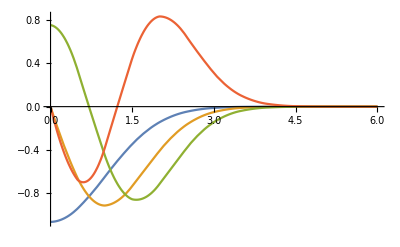

```mathematica
egnVec=Riffle[egnVec1,egnVec2];
Plot[Evaluate[egnVec],{x,0,6},PlotRange->All]
```

#### Landau levels (Landau gauge)

Check for the parabolic dispersion: equidistant energy levels, energy does not depend on p^y

```mathematica
NDEigensystem[-1/2 D[ψ[x], x,x]+1/2(1-x)^2 ψ[x],ψ[x],{x,-10,10},4];
%[[1]]
NDEigensystem[-1/2 D[ψ[x], x,x]+1/2(2-x)^2 ψ[x],ψ[x],{x,-10,10},4];
%[[1]]
```

{0.501189,1.50696,2.53003,3.53334}

{0.501189,1.50696,2.53003,3.53334}

### (Weyl semimetal) Landau levels transition into surface states using the method of mirror images -- SEEMS to be an incorrect approach (because not only wavefunction is continuous across the interface, but its first derivative as well -- this we did not ask for!)

Distances are measured in units of magnetic length, Fermi velocity of the bulk particles is set to 1

For large enough separation of parabolas, states do not talk to each other, zeroth Landua level has zero energy, for non-zero Landau levels there is two-fold degeneracy (so one has to take the appropritate linear superposition of them)

That the eigenvalue of the n=1 level is 2 is in agreement with the expected dispersion relation ϵ = sqrt(pz^2 + 2/l_B^2)

{0.000597761,2.0006,2.28924,4.28924,4.3388}

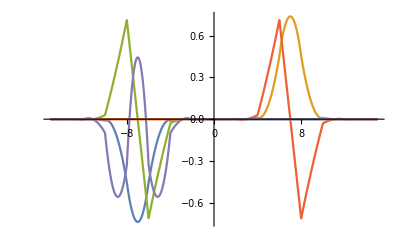

```mathematica
{egnVal1,egnVec1}=NDEigensystem[{-Laplacian[χ[x],{x}]+(Abs[x]-py)^2 χ[x]+Sign[x]χ[x],DirichletCondition[χ[x]==0,True]}/.py->7,χ[x],{x,-20,20},5];
egnVal1
Plot[egnVec1,{x,-15,15},PlotRange->All]
```

But if we make the parabolas closer to each other (and to the surface), the energy of the “zeroth Landau level” goes away from 0, and the energy degeneracy of the higher levels gets broken. At the same time, the energy gap of order 1/l_B between the n=0 and higher levels remains

{0.00261396,1.90001,2.10502}

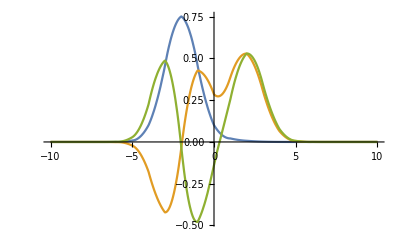

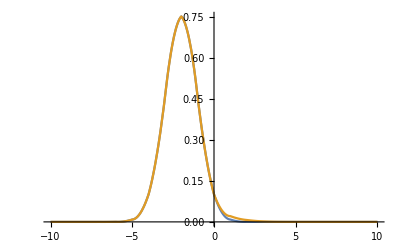

```mathematica
{egnVal1,egnVec1}=NDEigensystem[{-Laplacian[χ[x],{x}]+(Abs[x]-py)^2 χ[x]+Sign[x]χ[x],DirichletCondition[χ[x]==0,True]}/.py->2,χ[x],{x,-10,10},3];
egnVal1
Plot[egnVec1,{x,-10,10},PlotRange->All]

{egnValnoSurface,egnVecnoSurface}=NDEigensystem[{-Laplacian[χ[x],{x}]+(x+py)^2 χ[x]-χ[x],DirichletCondition[χ[x]==0,True]}/.py->2,χ[x],{x,-10,10},1];
Plot[{egnVecnoSurface[[1]],egnVec1[[1]]},{x,-10,10},PlotRange->All]
```

{0.693205,3.12232,4.97719}

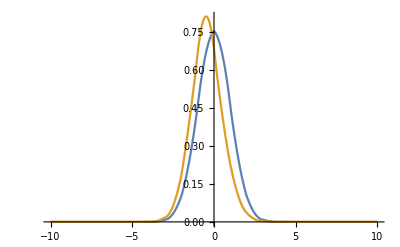

```mathematica
{egnVal1,egnVec1}=NDEigensystem[{-Laplacian[χ[x],{x}]+(Abs[x]-py)^2 χ[x]+Sign[x]χ[x],DirichletCondition[χ[x]==0,True]}/.py->0,χ[x],{x,-10,10},3];
egnVal1

{egnValnoSurface,egnVecnoSurface}=NDEigensystem[{-Laplacian[χ[x],{x}]+(x+py)^2 χ[x]-χ[x],DirichletCondition[χ[x]==0,True]}/.py->0,χ[x],{x,-10,10},1];
Plot[{-egnVecnoSurface[[1]],egnVec1[[1]]},{x,-10,10},PlotRange->All]
```

#### Landau levels transition into surface states using the (Weyl semimetal) : no mirror images

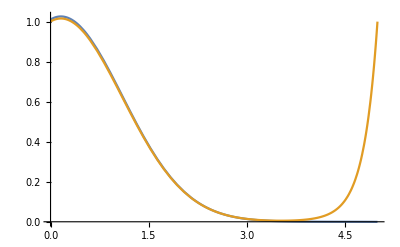

```mathematica
sol1=NDSolve[{-u''[x]+(x^2-1)u[x]==0.2u[x],u[0]==1,u[5]==0},u[x],{x,0,5}];
sol2=NDSolve[{-u''[x]+(x^2-1)u[x]==0.2u[x],u[0]==1,u[5]==1},u[x],{x,0,5}];
Plot[{1.01u[x]/.sol1,u[x]/.sol2},{x,0,5}]
```

```mathematica
NDSolve[{-u''[x]+(x^2-1)u[x]==0.2u[x],u[0]==1,u[5]==0},u[x],{x,0,5}]
```

{{u[x]→InterpolatingFunction[{{0., 5.}}, <>][x]}}

## Landau level -- Fermi arc hybridization in a Weyl semimetal

### BBL set-1 (TODO: include vzcorr in the dispersion relation)

#### BBL parameters

```mathematica
NSolve[{(b0/bz Sin[pz])^2+2Cos[pz](1+M0)-(1+(1+M0)^2-(bz^2-b0^2)/4)==0}/.bz->1.2/.b0->0.2/.M0->-0.3,{pz}]
BBLSubstitution={bz->1.2,b0->0.2,M0->-0.3,pzWR->pz/.%[[1]],ϵ0R->-0.2/1.2 Sin[pz]/.%[[1]],ϵ0L->+0.2/1.2 Sin[pz]/.%[[1]]}
Subscript[v, perp]=Sqrt[4(bz^2-b0^2)/(bz^2-4 ϵ0R^2)]/.BBLSubstitution
Subscript[v, parallel]=1/(2(bz^2-4 ϵ0R^2))Sqrt[2^2(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR])^2+4(bz^2-4 ϵ0R^2)(4(Sin[pzWR])^2(1+M0)^2-b0^2(Cos[pzWR])^2)]/.BBLSubstitution

vzcorr=(-2(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR]))/(2(bz^2-4 ϵ0R^2))/.BBLSubstitution
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{pz→-0.631101},{pz→0.-4.59689 ⅈ},{pz→0.+4.59689 ⅈ},{pz→0.631101}}

{bz→1.2,b0→0.2,M0→-0.3,pzWR→-0.631101,ϵ0R→0.0983391,ϵ0L→-0.0983391}

1.99906

0.684712

-0.0223398

```mathematica
lB=20;
```

#### Dispersion relation of right-chiral surface states

```mathematica
DispersionRelationSurfR=Sqrt[2] Subscript[t, 2] Subscript[v, perp]/lB ParabolicCylinderD[lB^2/Subscript[v, perp]^2((ϵ-ϵ0R)^2-Subscript[v, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(ϵ-ϵ0R+Subscript[v, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[v, perp]^2((ϵ-ϵ0R)^2-Subscript[v, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.BBLSubstitution/.Subscript[t, 2]->-0.848;
dPzMin=ϵ0R/Subscript[v, parallel]/.BBLSubstitution
```

0.143621

The level bending takes place

```mathematica
FindRoot[DispersionRelationSurfR/.dPz->0.01/.py->-0.3,{ϵ,0.1}];
(ϵ-(ϵ0R-Subscript[v, parallel] dPz))/.dPz->0.01/.BBLSubstitution/.%
FindRoot[DispersionRelationSurfR/.dPz->0.01/.py->-0.2,{ϵ,0.1}];
(ϵ-(ϵ0R-Subscript[v, parallel] dPz))/.dPz->0.01/.BBLSubstitution/.%
FindRoot[DispersionRelationSurfR/.dPz->0.01/.py->-0.1,{ϵ,0.1}];
(ϵ-(ϵ0R-Subscript[v, parallel] dPz))/.dPz->0.01/.BBLSubstitution/.%
```

5.55112×10^-17

5.46363×10^-9

0.000906275

Looks like Fermi arc

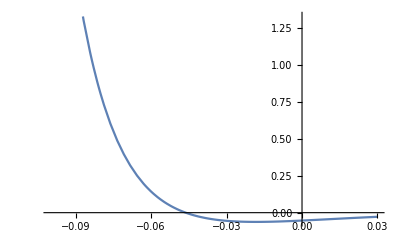

{py→-0.0462608}

```mathematica
Plot[DispersionRelationSurfR/.dPz->0.3/.ϵ->0,{py,-0.1,0.03}]
FindRoot[DispersionRelationSurfR/.dPz->0.3/.ϵ->0,{py,-0.1}]
```

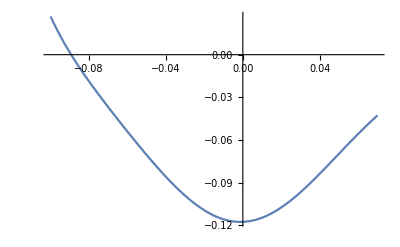

{py→-0.0892967}

```mathematica
Plot[DispersionRelationSurfR/.dPz->0.15/.ϵ->0,{py,-0.1,0.07}]
FindRoot[DispersionRelationSurfR/.dPz->0.15/.ϵ->0,{py,-0.1}]
```

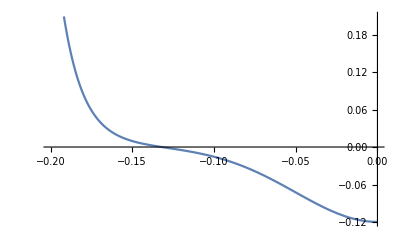

{py→-0.132036}

```mathematica
Plot[DispersionRelationSurfR/.dPz->dPzMin+10^-4/.ϵ->0,{py,-0.2,0}]
FindRoot[DispersionRelationSurfR/.dPz->dPzMin+10^-4/.ϵ->0,{py,-0.1}]
```

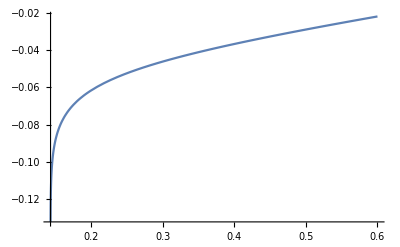

-0.132036

-0.185228

```mathematica
pyFermiR[dPzVar_]:=py/.FindRoot[DispersionRelationSurfR/.dPz->dPzVar/.ϵ->0,{py,-0.1}]
Plot[pyFermiR[dPz],{dPz,dPzMin+10^-4,0.6},PlotRange->All]
pyFermiR[dPzMin+10^-4]
pyFermiR[dPzMin+10^-7]
```

The velocity comes close enough to the expected asymptotic value of the B=0 FAs

-0.650416

-0.648022

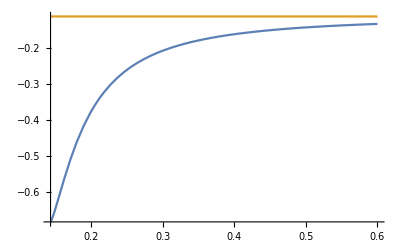

```mathematica
dEOdPzR[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRelationSurfR/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiR[dPzVar],{ϵ,0}]
dEOdPzR[0.15,0.001]
dEOdPzR[0.15,0.01]
Plot[{dEOdPzR[dPzVar,10^-4],-(1-Subscript[t, 2]^2)/(1+Subscript[t, 2]^2)Subscript[v, parallel]/.Subscript[t, 2]->-0.848},{dPzVar,dPzMin+10^-5,0.6},PlotRange->All]
```

#### Analysis of the boundary states for left-chiral node

```mathematica
DispersionRelationSurfL=Sqrt[2](-1/Subscript[t, L])Subscript[v, perp]/lB ParabolicCylinderD[lB^2/Subscript[v, perp]^2((ϵ-ϵ0L)^2-Subscript[v, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(ϵ-ϵ0L-Subscript[v, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[v, perp]^2((ϵ-ϵ0L)^2-Subscript[v, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.BBLSubstitution/.Subscript[t, L]->+0.848;
dPzMax=-ϵ0L/Subscript[v, parallel]/.BBLSubstitution
```

0.143621

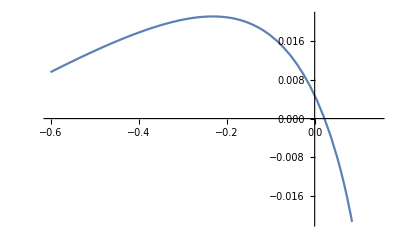

```mathematica
pyFermiL[dPzVar_]:=py/.FindRoot[DispersionRelationSurfL/.dPz->dPzVar/.ϵ->0.,{py,-0.1}]
Plot[pyFermiL[dPz],{dPz,-0.6,dPzMax-10^-3}]
```

```mathematica
dEOdPzL[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRelationSurfL/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiL[dPzVar],{ϵ,0}]
dEOdPzL[0.1,-0.001]
dEOdPzL[0.1,-0.01]
```

0.569055

0.565465

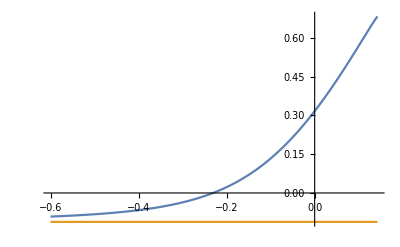

```mathematica
Plot[{dEOdPzL[dPzVar,-0.001],-(1-Subscript[t, 2]^2)/(1+Subscript[t, 2]^2)Subscript[v, parallel]/.Subscript[t, 2]->-0.848},{dPzVar,-0.6,dPzMax-10^-3},PlotRange->All]
```

#### Total contribution of L+R (TO CHECK: does the y-velocity all the time remains positive?)

The (approximate) cancellation happens

```mathematica
Quiet@NIntegrate[dEOdPzR[dPzVar,10^-3],{dPzVar,dPzMin+10^-3,-pzWR/.BBLSubstitution}]
Quiet@NIntegrate[dEOdPzL[dPzVar,-10^-3],{dPzVar,pzWR/.BBLSubstitution,dPzMax-10^-3}]
Quiet@(NIntegrate[dEOdPzR[dPzVar,10^-3],{dPzVar,dPzMin+10^-3,-pzWR/.BBLSubstitution}]+NIntegrate[dEOdPzL[dPzVar,-10^-3],{dPzVar,pzWR/.BBLSubstitution,dPzMax-10^-3}])
```

-0.106448

0.0742305

-0.0322171

How does the answer change if we calculate the derivative wrt p^z with less accuracy?

```mathematica
Quiet@(NIntegrate[dEOdPzR[dPzVar,10^-2],{dPzVar,dPzMin+10^-2,-pzWR/.BBLSubstitution}]+NIntegrate[dEOdPzL[dPzVar,-10^-2],{dPzVar,pzWR/.BBLSubstitution,dPzMax-10^-2}])
```

-0.0334487

How does the answer change if we vary the distribution between the left and right integration limits?

```mathematica
Quiet@(NIntegrate[dEOdPzR[dPzVar,10^-3],{dPzVar,dPzMin+10^-3,-0.1-pzWR/.BBLSubstitution}]+NIntegrate[dEOdPzL[dPzVar,-10^-3],{dPzVar,-0.1+pzWR/.BBLSubstitution,dPzMax-10^-3}])
```

-0.028383

#### Contribution of the n=1 LL (TO REVISE)

Let us shift the chemical potential from ϵ = 0

```mathematica
dPzMax2=0.2;
ϵF2=ϵ0L+Sqrt[Subscript[v, parallel]^2 dPz^2+2 Subscript[v, perp]^2/lB^2]/.dPz->dPzMax2/.BBLSubstitution
ϵ0L+Sqrt[2 2 Subscript[v, perp]^2/lB^2]/.dPz->0.1/.BBLSubstitution
```

0.0984715

0.101567

Only n=0 LL crosses the Fermi level

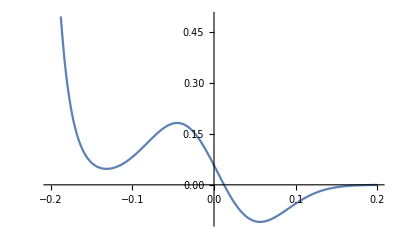

```mathematica
Plot[DispersionRelationSurfL/.dPz->dPzMax2+10^-3/.ϵ->ϵF2,{py,-0.2,0.2}]
```

n=1 LL just starts to cross the Fermi level

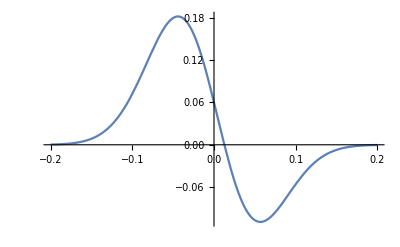

```mathematica
Plot[DispersionRelationSurfL/.dPz->dPzMax2/.ϵ->ϵF2,{py,-0.2,0.2}]
```

Both n=0 and n=1 LLs cross the Fermi level

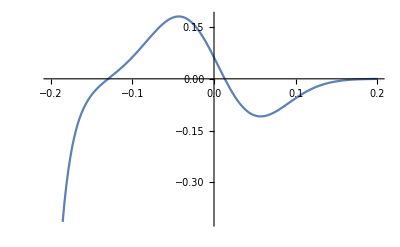

```mathematica
Plot[DispersionRelationSurfL/.dPz->dPzMax2-10^-3/.ϵ->ϵF2,{py,-0.2,0.2}]
```

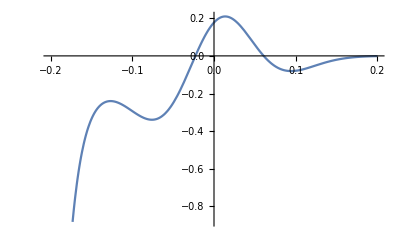

```mathematica
Plot[DispersionRelationSurfL/.dPz->0./.ϵ->ϵF2,{py,-0.2,0.2}]
```

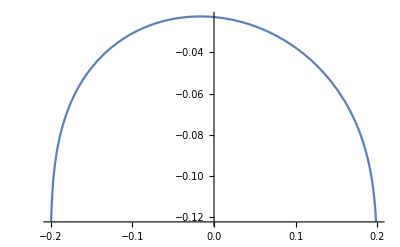

```mathematica
pyFermiL2[dPzVar_]:=py/.FindRoot[DispersionRelationSurfL/.dPz->dPzVar/.ϵ->ϵF2,{py,-0.05}]
Plot[pyFermiL2[dPz],{dPz,-dPzMax2,dPzMax2}]
```

```mathematica
dEOdPzL2[dPzVar_,dPzIncrement_]:=(ϵ-ϵF2)/dPzIncrement/.FindRoot[DispersionRelationSurfL/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiL2[dPzVar],{ϵ,ϵF2}]
dEOdPzL2[0.06,-0.0001]
dEOdPzL2[0.06,-0.001]
```

0.17753

0.176554

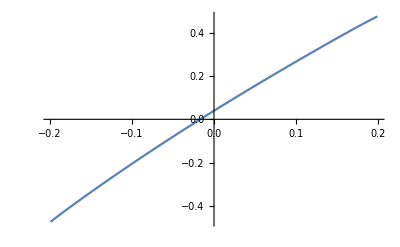

0.010935

0.0109708

```mathematica
Plot[dEOdPzL2[dPzVar,-10^-4],{dPzVar,-dPzMax2+10^-3,dPzMax2-10^-3}]
Quiet@NIntegrate[dEOdPzL2[dPzVar,-10^-4],{dPzVar,-dPzMax2+10^-3,dPzMax2-10^-3}]
Quiet@NIntegrate[dEOdPzL2[dPzVar,-10^-5],{dPzVar,-dPzMax2+10^-3,dPzMax2-10^-3}]
```

### BBL set-2

#### Set-2

```mathematica
NSolve[{(b0/bz Sin[pz])^2+2Cos[pz](1+M0)-(1+(1+M0)^2-(bz^2-b0^2)/4)==0}/.bz->1.2/.b0->0.1/.M0->-0.3,{pz}]
BBLSet2={bz->1.2,b0->0.1,M0->-0.3,pzWR->pz/.%[[1]],ϵ0R->-0.1/1.2 Sin[pz]/.%[[1]],ϵ0L->+0.1/1.2 Sin[pz]/.%[[1]]}
Subscript[vSet2, perp]=Sqrt[4(bz^2-b0^2)/(bz^2-4 ϵ0R^2)]/.BBLSet2
Subscript[vSet2, parallel]=1/(2(bz^2-4 ϵ0R^2))Sqrt[2^2(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR])^2+4(bz^2-4 ϵ0R^2)(4(Sin[pzWR])^2(1+M0)^2-b0^2(Cos[pzWR])^2)]/.BBLSet2
vzcorrSet2=(-(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR]))/(bz^2-4 ϵ0R^2)/.BBLSet2
dPzMinSet2=ϵ0R/(Subscript[vSet2, parallel]-vzcorrSet2)/.BBLSet2
dPzMaxSet2=-ϵ0L/(Subscript[vSet2, parallel]+vzcorrSet2)/.BBLSet2
(*This value of Subscript[t, R] was found in Vazifeh-Franz.nb*)
tRSet2=-0.92;
tLSet2=-tRSet2;
(*This is the parameter that enters Energy = ... + vzQuadraticCorrectionSet2×pz^3 *)
lB=50;
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{pz→-0.631403},{pz→0.-5.99541 ⅈ},{pz→0.+5.99541 ⅈ},{pz→0.631403}}

{bz→1.2,b0→0.1,M0→-0.3,pzWR→-0.631403,ϵ0R→0.0491898,ϵ0L→-0.0491898}

1.99978

0.687765

-0.0108816

0.0704073

0.072671

The values of velocity agree with KWANT, provided that we choose proper vzQuadraticCorrectionSet2

```mathematica
(*So far, the parameter is extracted manually from KWANT, and in principle it can depend on the boundary condition, in particular on tRSet2*)
vzQuadraticCorrectionSet2 = -1.3×10^-2;
-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2
-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2+3vzQuadraticCorrectionSet2 dPz^2/.dPz->pzWR/.BBLSet2
```

-0.0680961

-0.0836442

#### Dispersion relation of right-chiral states

```mathematica
DispersionRSet2=Sqrt[2]tRSet2 Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ+Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0R-vzcorrSet2 dPz-vzQuadraticCorrectionSet2 dPz^3/.BBLSet2;
```

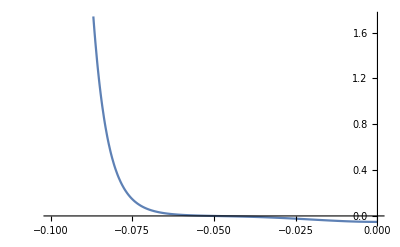

{py→-0.0502242}

```mathematica
Plot[DispersionRSet2/.dPz->dPzMinSet2+10^-4/.ϵ->0,{py,-0.1,0}]
FindRoot[DispersionRSet2/.dPz->dPzMinSet2+10^-4/.ϵ->0,{py,-0.1}]
```

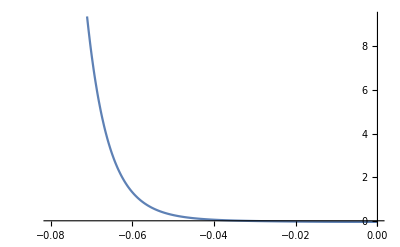

{py→-0.0326948}

```mathematica
Plot[DispersionRSet2/.dPz->0.08/.ϵ->0,{py,-0.08,0}]
FindRoot[DispersionRSet2/.dPz->0.08/.ϵ->0,{py,-0.1}]
```

Looks like Fermi arc

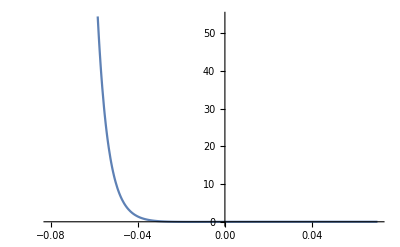

{py→-0.0236644}

```mathematica
Plot[DispersionRSet2/.dPz->0.15/.ϵ->0,{py,-0.08,0.07}]
FindRoot[DispersionRSet2/.dPz->0.15/.ϵ->0,{py,-0.1}]
```

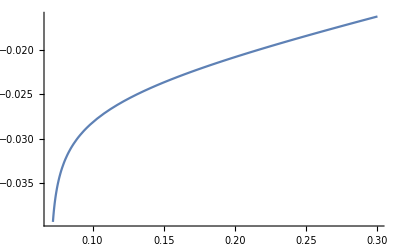

-0.0502242

-0.0597398

```mathematica
pyFermiRSet2[dPzVar_]:=py/.FindRoot[DispersionRSet2/.dPz->dPzVar/.ϵ->0,{py,-0.1}]
Plot[pyFermiRSet2[dPzVar],{dPzVar,dPzMinSet2+10^-4,0.3}]
pyFermiRSet2[dPzMinSet2+10^-4]
pyFermiRSet2[dPzMinSet2+10^-7]
```

-0.128802

-0.125072

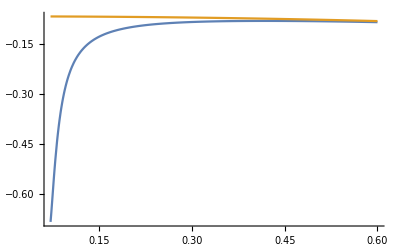

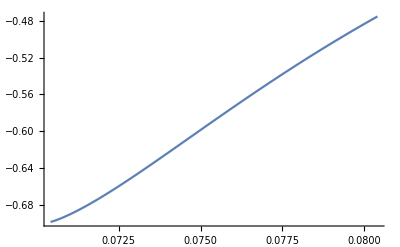

```mathematica
dEOdPzRSet2[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRSet2/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiRSet2[dPzVar],{ϵ,0}]
dEOdPzRSet2[0.15,0.001]
dEOdPzRSet2[0.15,0.01]
Plot[{dEOdPzRSet2[dPzVar,0.001],-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2+3vzQuadraticCorrectionSet2 dPzVar^2},{dPzVar,dPzMinSet2+10^-3,0.6},PlotRange->All]
Plot[dEOdPzRSet2[dPzVar,10^-4],{dPzVar,dPzMinSet2+10^-5,dPzMinSet2+10^-2}]
```

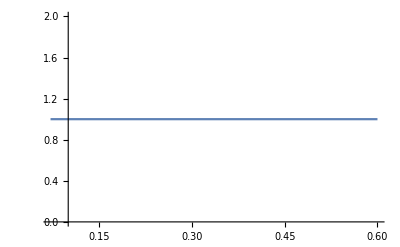

```mathematica
SignRSet2[dPzVar_]:=Sign[ϵ]/.FindRoot[DispersionRSet2/.dPz->dPzVar/.py->pyFermiRSet2[dPzVar]+10^-3,{ϵ,0}]
Plot[SignRSet2[dPzVar],{dPzVar,dPzMinSet2+10^-3,0.6},PlotRange->All]
```

#### Left chirality

```mathematica
DispersionLSet2=Sqrt[2](-1/tLSet2)Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ-Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0L-vzcorrSet2 dPz-vzQuadraticCorrectionSet2 dPz^3/.BBLSet2;
```

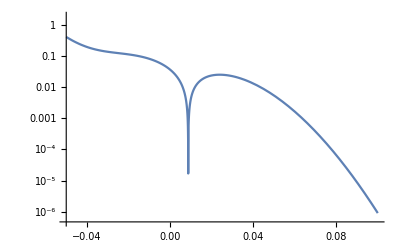

{py→0.00874329}

```mathematica
LogPlot[Abs[DispersionLSet2]/.dPz->0./.ϵ->0,{py,-0.05,0.1}]
FindRoot[DispersionLSet2/.dPz->0./.ϵ->0,{py,-0.01}]
```

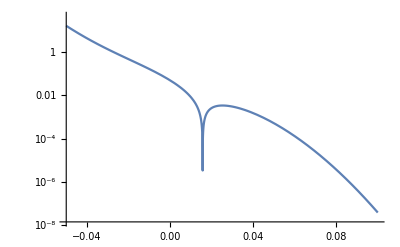

{py→0.0156826}

```mathematica
LogPlot[Abs[DispersionLSet2]/.dPz->-0.1/.ϵ->0,{py,-0.05,0.1}]
FindRoot[DispersionLSet2/.dPz->-0.1/.ϵ->0,{py,-0.01}]
```

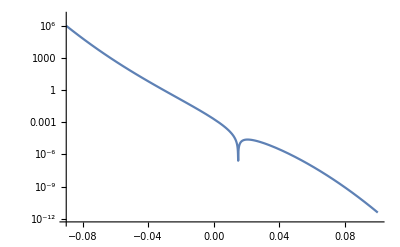

{py→0.0148529}

```mathematica
LogPlot[Abs[DispersionLSet2]/.dPz->-0.2/.ϵ->0,{py,-0.09,0.1}]
FindRoot[DispersionLSet2/.dPz->-0.2/.ϵ->0,{py,-0.01}]
```

Why p^yF is non-monotonic?

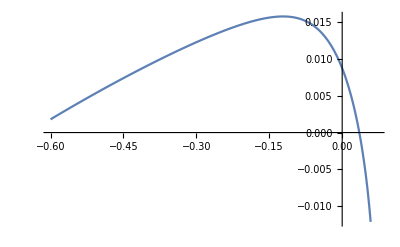

```mathematica
pyFermiLSet2[dPzVar_]:=py/.FindRoot[DispersionLSet2/.dPz->dPzVar/.ϵ->0,{py,-0.01}]
Plot[pyFermiLSet2[dPzVar],{dPzVar,-0.6,dPzMaxSet2-10^-4}]
```

0.115939

0.12735

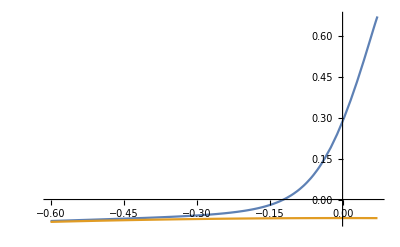

```mathematica
dEOdPzLSet2[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionLSet2/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiLSet2[dPzVar],{ϵ,0}]
dEOdPzLSet2[-0.05,0.001]
dEOdPzLSet2[-0.05,0.01]
Plot[{dEOdPzLSet2[dPzVar,-0.001],-(1-tLSet2^2)/(1+tLSet2^2)Subscript[vSet2, parallel]+vzcorrSet2+3vzQuadraticCorrectionSet2 dPzVar^2},{dPzVar,-0.6,dPzMaxSet2-10^-3},PlotRange->All]
```

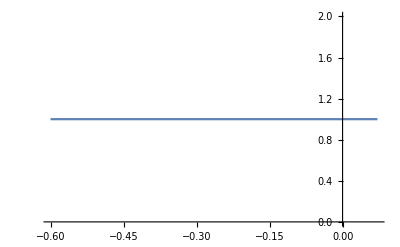

```mathematica
SignLSet2[dPzVar_]:=Sign[ϵ]/.FindRoot[DispersionLSet2/.dPz->dPzVar/.py->pyFermiLSet2[dPzVar]+10^-3,{ϵ,0}]
Plot[SignLSet2[dPzVar],{dPzVar,-0.6,dPzMaxSet2-10^-3},PlotRange->All]
```

#### Total contribution of L+R to the current

```mathematica
IZRSet2=Quiet@NIntegrate[SignRSet2[dPzVar] dEOdPzRSet2[dPzVar,10^-3],{dPzVar,dPzMinSet2+10^-3,-pzWR/.BBLSet2}]
IZLSet2=Quiet@NIntegrate[SignLSet2[dPzVar]dEOdPzLSet2[dPzVar,-10^-3],{dPzVar,pzWR/.BBLSet2,dPzMaxSet2-10^-3}]
IZRSet2+IZLSet2
```

-0.0626142

0.0162444

-0.0463697

While the BBL’16 gives the prefactor close to

```mathematica
-ϵ0R/.BBLSet2
```

-0.0491898

Reducing the precision in the calculation of the z-velocity does not change the result significantly

```mathematica
temp280117=Quiet@NIntegrate[SignRSet2[dPzVar] dEOdPzRSet2[dPzVar,10^-2],{dPzVar,dPzMinSet2+10^-3,-pzWR/.BBLSet2}]
Quiet@NIntegrate[SignLSet2[dPzVar]dEOdPzLSet2[dPzVar,-10^-2],{dPzVar,pzWR/.BBLSet2,dPzMaxSet2-10^-3}]
temp280117+%
```

-0.0611597

0.013955

-0.0472046

#### Calculation restricted to the domain of the effective theory (vzQuadratic=0) + assumption of the p^y- p^z separability of the FA energy: again we are close to -1/2!

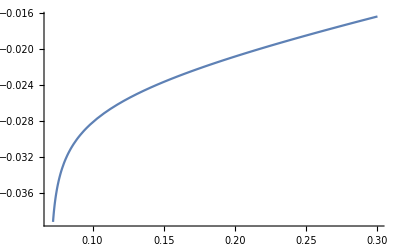

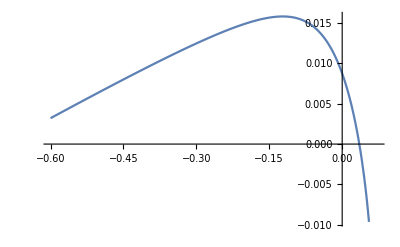

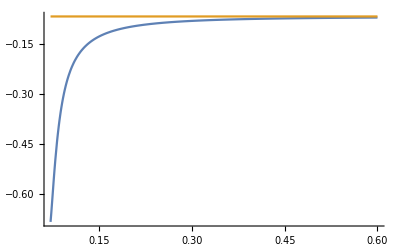

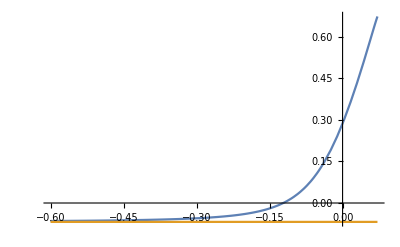

```mathematica
DispersionRMinSet2=Sqrt[2]tRSet2 Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ+Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0R-vzcorrSet2 dPz/.BBLSet2;
DispersionLMinSet2=Sqrt[2](-1/tLSet2)Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ-Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0L-vzcorrSet2 dPz/.BBLSet2;
pyFermiRMinSet2[dPzVar_]:=py/.FindRoot[DispersionRMinSet2/.dPz->dPzVar/.ϵ->0,{py,-0.1}]
Plot[pyFermiRMinSet2[dPzVar],{dPzVar,dPzMinSet2+10^-4,0.3}]
pyFermiLMinSet2[dPzVar_]:=py/.FindRoot[DispersionLMinSet2/.dPz->dPzVar/.ϵ->0,{py,-0.01}]
Plot[pyFermiLMinSet2[dPzVar],{dPzVar,-0.6,dPzMaxSet2-10^-4}]
dEOdPzRMinSet2[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRMinSet2/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiRMinSet2[dPzVar],{ϵ,0}]
Plot[{dEOdPzRMinSet2[dPzVar,0.001],-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2},{dPzVar,dPzMinSet2+10^-3,0.6},PlotRange->All]
dEOdPzLMinSet2[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionLMinSet2/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiLMinSet2[dPzVar],{ϵ,0}]
Plot[{dEOdPzLMinSet2[dPzVar,-0.001],-(1-tLSet2^2)/(1+tLSet2^2)Subscript[vSet2, parallel]+vzcorrSet2},{dPzVar,-0.6,dPzMaxSet2-10^-3},PlotRange->All]
```

Now we calculate the current in the effective theory, and for the UV-completion we say that the FA energy is SEPARABLE into the sum of functions of py and pz only

```mathematica
dPzCutR=0.3;
dPzCutL=-0.3;
IZRCutSet2=Quiet@NIntegrate[dEOdPzRMinSet2[dPzVar,10^-3],{dPzVar,dPzMinSet2+10^-3,dPzCutR}]
IZLCutSet2=Quiet@NIntegrate[dEOdPzLMinSet2[dPzVar,-10^-3],{dPzVar,dPzCutL,dPzMaxSet2-10^-3}]
IZRCutSet2+IZLCutSet2+(ϵ0L+(-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutL)-(ϵ0R+(-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutR)/.BBLSet2
```

-0.0347186

0.0400499

-0.0521907

The result gets changed not significantly when we cut more of the effective-theory region

```mathematica
dPzCutR=0.2;
dPzCutL=-0.2;
IZRCutSet2=Quiet@NIntegrate[dEOdPzRMinSet2[dPzVar,10^-3],{dPzVar,dPzMinSet2+10^-3,dPzCutR}]
IZLCutSet2=Quiet@NIntegrate[dEOdPzLMinSet2[dPzVar,-10^-3],{dPzVar,dPzCutL,dPzMaxSet2-10^-3}]
IZRCutSet2+IZLCutSet2+(ϵ0L+(-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutL)-(ϵ0R+(-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutR)/.BBLSet2
```

-0.0258763

0.0449177

-0.0520999

#### Calculation of I^z in the effective theory with DEFORMED boundary condition: the prefactor is different by 20%!

The total velocity of the Fermi arc in the vicinity of a node was extracted from KWANT (the on-site Hamiltonians of the boundary and the next-to-boundary sites were rescaled by 3 times)

```mathematica
vzArcTotBoundDef=0.039;
tRSet2BoundDef=-Sqrt[(Subscript[vSet2, parallel]-(vzcorrSet2-vzArcTotBoundDef))/(Subscript[vSet2, parallel]+(vzcorrSet2-vzArcTotBoundDef))]
tLSet2BoundDef=-tRSet2BoundDef;
```

-1.07536

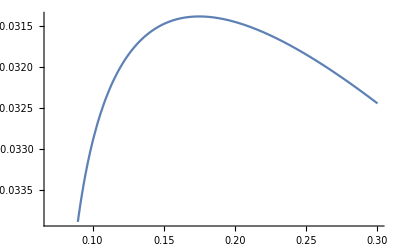

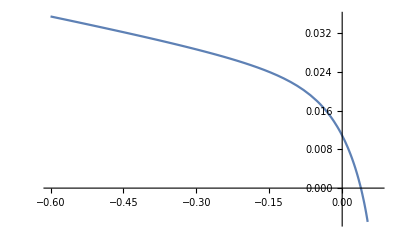

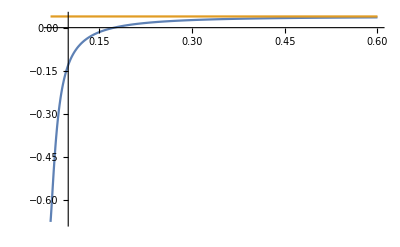

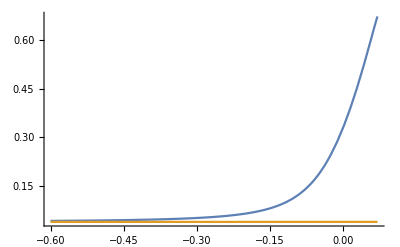

```mathematica
DispersionRMinSet2BoundDef=Sqrt[2]tRSet2BoundDef Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ+Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0R-vzcorrSet2 dPz/.BBLSet2;
DispersionLMinSet2BoundDef=Sqrt[2](-1/tLSet2BoundDef)Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ-Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0L-vzcorrSet2 dPz/.BBLSet2;
pyFermiRMinSet2BoundDef[dPzVar_]:=py/.FindRoot[DispersionRMinSet2BoundDef/.dPz->dPzVar/.ϵ->0,{py,-0.1}]
Plot[pyFermiRMinSet2BoundDef[dPzVar],{dPzVar,dPzMinSet2+10^-4,0.3}]
pyFermiLMinSet2BoundDef[dPzVar_]:=py/.FindRoot[DispersionLMinSet2BoundDef/.dPz->dPzVar/.ϵ->0,{py,-0.01}]
Plot[pyFermiLMinSet2BoundDef[dPzVar],{dPzVar,-0.6,dPzMaxSet2-10^-4}]

dEOdPzRMinSet2BoundDef[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRMinSet2BoundDef/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiRMinSet2BoundDef[dPzVar],{ϵ,0}]
Plot[{dEOdPzRMinSet2BoundDef[dPzVar,0.001],-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2},{dPzVar,dPzMinSet2+10^-3,0.6},PlotRange->All]
dEOdPzLMinSet2BoundDef[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionLMinSet2BoundDef/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiLMinSet2BoundDef[dPzVar],{ϵ,0}]
Plot[{dEOdPzLMinSet2BoundDef[dPzVar,-0.001],-(1-tLSet2BoundDef^2)/(1+tLSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2},{dPzVar,-0.6,dPzMaxSet2-10^-3},PlotRange->All]
```

```mathematica
dPzCutRBoundDef=0.3;
dPzCutLBoundDef=-0.3;
IZRCutSet2BoundDef=Quiet@NIntegrate[dEOdPzRMinSet2BoundDef[dPzVar,10^-3],{dPzVar,dPzMinSet2+10^-3,dPzCutRBoundDef}]
IZLCutSet2BoundDef=Quiet@NIntegrate[dEOdPzLMinSet2BoundDef[dPzVar,-10^-3],{dPzVar,dPzCutLBoundDef,dPzMaxSet2-10^-3}]
IZRCutSet2BoundDef+IZLCutSet2BoundDef+(ϵ0L+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutLBoundDef)-(ϵ0R+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutRBoundDef)/.BBLSet2
```

-0.00996351

0.0685952

-0.0631479

Reduction of the p^z-range of the effective theory does not change the result significantly

```mathematica
dPzCutRBoundDef=0.2;
dPzCutLBoundDef=-0.2;
IZRCutSet2BoundDef=Quiet@NIntegrate[dEOdPzRMinSet2BoundDef[dPzVar,10^-3],{dPzVar,dPzMinSet2+10^-3,dPzCutRBoundDef}]
IZLCutSet2BoundDef=Quiet@NIntegrate[dEOdPzLMinSet2BoundDef[dPzVar,-10^-3],{dPzVar,dPzCutLBoundDef,dPzMaxSet2-10^-3}]
IZRCutSet2BoundDef+IZLCutSet2BoundDef+(ϵ0L+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutLBoundDef)-(ϵ0R+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutRBoundDef)/.BBLSet2
```

-0.0119558

0.0629385

-0.0629969

Reduction of the precision in calculation of the z-velocity also does not alter the result significantly

```mathematica
dPzCutRBoundDef=0.2;
dPzCutLBoundDef=-0.2;
IZRCutSet2BoundDef=Quiet@NIntegrate[dEOdPzRMinSet2BoundDef[dPzVar,10^-2],{dPzVar,dPzMinSet2+10^-3,dPzCutRBoundDef}]
IZLCutSet2BoundDef=Quiet@NIntegrate[dEOdPzLMinSet2BoundDef[dPzVar,-10^-2],{dPzVar,dPzCutLBoundDef,dPzMaxSet2-10^-3}]
IZRCutSet2BoundDef+IZLCutSet2BoundDef+(ϵ0L+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutLBoundDef)-(ϵ0R+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutRBoundDef)/.BBLSet2
```

-0.0101709

0.0612901

-0.0628604

#### Estimate of the non-separability of the FA dispersion in the UV region, and its influence on the I^z prefactor: the “correction” does not seem to be small!

Here we use the parameters extracted from BBL-set-2.ipynb by MacLaurin expansion of the FA dispersion, for the BBL set-2 and for the deformed boundary condition (for the original b.c., we know that the FA dispersion is separable, although the reason is not clear)

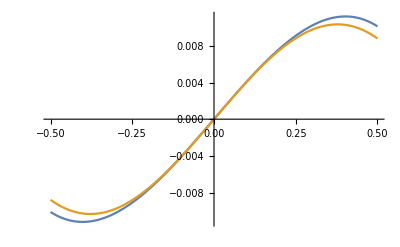

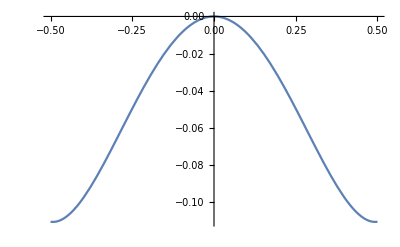

FindRoot::nlnum: The function value {-0.527033-0.2265 PzVar+0.4674 PzVar^3} is not a list of numbers with dimensions {1} at {py} = {-0.1}.

ReplaceAll::reps: {FindRoot[C10 Pz+C30 Pz^3+C01 py+C03 py^3/.Pz→PzVar,{py,-0.1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.527033-0.2265 PzVar+0.4674 PzVar^3} is not a list of numbers with dimensions {1} at {py} = {-0.1}.

ReplaceAll::reps: {FindRoot[C10 Pz+C30 Pz^3+C01 py+C03 py^3/.Pz→PzVar,{py,-0.1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.527033-0.2265 PzVar+0.4674 PzVar^3} is not a list of numbers with dimensions {1} at {py} = {-0.1}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[C10 Pz+C30 Pz^3+C01 py+C03 py^3/.Pz→PzVar,{py,-0.1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-0.0524682

```mathematica
C10=-0.2265;
C30=0.4674;
C01=5.417;
C03=-14.667;
C21=-10.947;
C12=3.056;
pyFermi0UVSet2BoundDef[PzVar_]:=py/.FindRoot[C10 Pz+C30 Pz^3+C01 py + C03 py^3/.Pz->PzVar,{py,-0.1}]
dPyUVSet2BoundDef[PzVar_]:=-(py pz(C21 py+C12 pz))/(C01+3C03 py^2)/.py->pyFermi0UVSet2BoundDef[PzVar]/.pz->PzVar
Plot[{pyFermi0UVSet2BoundDef[PzVar],pyFermi0UVSet2BoundDef[PzVar]+dPyUVSet2BoundDef[PzVar]},{PzVar,-0.5,0.5}]
Plot[C12 py^2+2C21 py PzVar/.py->pyFermi0UVSet2BoundDef[PzVar],{PzVar,-0.5,0.5}]
NIntegrate[C12 py^2+2C21 py PzVar/.py->pyFermi0UVSet2BoundDef[PzVar],{PzVar,-0.5,0.5}]
```